```mathematica
Integrate[1/(x^(3/2)y^(3/2)(1-x-y)^(3/2)),{y,(1-x)/2,x}]
```

ConditionalExpression[(-2+6 x)/(√(1-2 x) (-1+x)^2 x^2), ]

```mathematica
Integrate[(-2+6 x)/(√(1-2 x) (-1+x)^2 x^2),{x,1/3,a/2}]
```

ConditionalExpression[(4 √(1-a) (-2+3 a))/((-2+a) a)+2 π-12 ArcTan[√(1-a)], 0<Re[a]≤1||a∉ℝ]

```mathematica
(4 √(1-a) (-2+3 a))/((-2+a) a)+2 π-12 ArcTan[√(1-a)]/.a->1
```

2 π

```mathematica
FindRoot[(4 √(1-a) (-2+3 a))/((-2+a) a)+2 π-12 ArcTan[√(1-a)]-π,{a,0.95}]
```

{a→0.958053}

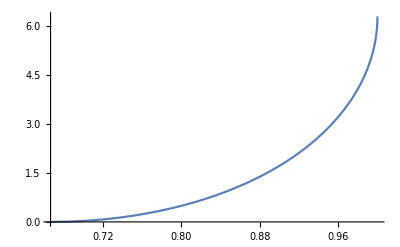

```mathematica
Plot[(4 √(1-a) (-2+3 a))/((-2+a) a)+2 π-12 ArcTan[√(1-a)],{a,2/3,1}]
```

```mathematica
a=0.9580531670784332;
NIntegrate[1/(x^(3/2)(1-x-y)^(3/2)z^(3/2)(y-z)^(3/2)),{x,1-a,a/2},{y,1-a/2-x,a/2},{z,a/2-x+0.01,1/2-x}]
```

26.8731

```mathematica
phi[alpha_]:=(4 √(1-alpha) (-2+3 alpha))/((-2+alpha)alpha)+2 π-12 ArcTan[√(1-alpha)];
```

```mathematica
psi[alpha_]:=NIntegrate[1/(x^(3/2)(1-x-y)^(3/2)z^(3/2)(y-z)^(3/2)),{x,1-alpha,alpha/2},{y,1-alpha/2-x,alpha/2},{z,alpha/2-x+0.01,1/2-x}];
```

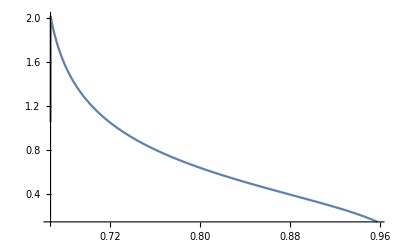

```mathematica
Plot[psi[a]/(32Sqrt[π]phi[a]),{a,2/3,0.9581}]
```

```mathematica
{psi[a]/(32Sqrt[π]phi[a]),phi[a],psi[a]}/.a->0.9580531670784332
```

NIntegrate::inumr: The integrand 1/(x^(3/2) (1-x-y)^(3/2) (y-z)^(3/2) z^(3/2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

{0.150814,3.14159,26.8731}